```mathematica
f[θ_,r_] := 1/(1+Exp[-β0-βθ*θ-βr*r]);
D[D[f[θ,r],r],θ]
Simplify[D[D[f[θ,r],r],θ]]
```

(2 ⅇ^(-2 β0-2 r βr-2 βθ θ) βr βθ)/((1+ⅇ^(-β0-r βr-βθ θ))^3)-(ⅇ^(-β0-r βr-βθ θ) βr βθ)/((1+ⅇ^(-β0-r βr-βθ θ))^2)

-(ⅇ^(β0+r βr+βθ θ) (-1+ⅇ^(β0+r βr+βθ θ)) βr βθ)/((1+ⅇ^(β0+r βr+βθ θ))^3)

```mathematica
Simplify[(a-b)/(a+b)^3]
```

(a-b)/(a+b)^3

```mathematica
Simplify[(a-1)*((1/a)+1)^3 - ((1/a)-a)*(a+1)^3]
```

((-1+a) (1+a)^3 (1+a^2+a^3))/a^3

```mathematica
Manipulate[
Plot[
Evaluate@ Table[1/(1+Exp[-β0-βθ*θ-βr*r]),{θ,-1,1,2}],
{r,-.5,5},
PlotLegends->Table[Row[{"θ=",θ}],{θ,-1,1,2}],PlotLabel->Row[{"β0=",β0,", βr=",βr,", β0=",β0}] ,AxesLabel->{"r","P(Success)"} 
],
{{β0,-4},-4,4},{{βr,0.1},0.1,4},{{βθ,1.25},0.1,4}]
```

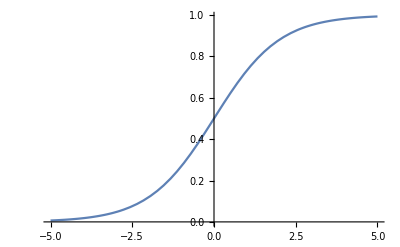

```mathematica
Plot[1/(1+Exp[-x]),{x,-5,5}]
```